```mathematica
l = 2;
m = 8;
B={4 (l+n-2) (l+n-1)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-8 l (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),2 (2 l^2-4 l n-4 n^2+1)/((l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),2 l (2 n+1) (2 l+2 n+1)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),(2 n+1) (2 n+3) (2 l+2 n+1) 
(2 l+2 n+3)/(4 (l+n) (l+n+1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4))};
rB[n_]=Table[B[[-i]]/.{n->n-(3-i)},{i,1,5}];
tmp=rB[m] Table[If[i≥ 0,JacobiP[i,-1/2,l-1/2,x],0],{i,m-2,m+2}];
If[m<2,tmp[[1]]=0]; If[m<1,tmp[[2]]=0]; If[m==0,tmp[[3]]=0];
rP=Total[tmp];
iPr[r_]=Integrate[4r Integrate[4 r/r^l Worland[r, m,l],r],r];
irP = iPr[√((x+1)/2)];
iP = Integrate[JacobiP[m,-1/2,l-1/2,x],x,x];

iP-rP//FullSimplify//Expand
(irP-rP)//FullSimplify//Expand
JacobiP[1,-1/2,l-1/2,x]
rec [n_]={2 (l+n)/((l+2 n) (l+2 n+1)),-2 l/((l+2 n-1) (l+2 n+1)),-(2 n-1) (2 l+2 n-1)/(2 (l+n-1) (l+2 n-1) (l+2 n))
};
cP1=-2/3 Total[rec[m]Table[If[i<0,0,JacobiP[i,-1/2,l-1/2,0]],{i,m+1,m-1,-1}]]
cP1 JacobiP[1,-1/2,l-1/2,x]//Expand
```

-429/524288+(715 x)/16384

3648931/4718592+(230945 x)/294912

1/2 (-2+3 x)

715/24576

-715/24576+(715 x)/16384

```mathematica
l = 2;
m = 8;
;
rB[n_]=Table[B[[-i]]/.{n->n-(3-i)},{i,1,5}];
tmp=rB[m] Table[If[i≥ 0,JacobiP[i,-1/2,l-1/2,x],0],{i,m-2,m+2}];
If[m<2,tmp[[1]]=0]; If[m<1,tmp[[2]]=0]; If[m==0,tmp[[3]]=0];
rP=Total[tmp];
iP=Integrate[D[JacobiP[m,-1/2,l-1/2,x],{x,2}],x,x];
iP-rP//FullSimplify//Expand
JacobiP[1,-1/2,l-1/2,x]
rec [n_]={2 (l+n)/((l+2 n) (l+2 n+1)),-2 l/((l+2 n-1) (l+2 n+1)),-(2 n-1) (2 l+2 n-1)/(2 (l+n-1) (l+2 n-1) (l+2 n))
};
cP1=-2/3 Total[rec[m]Table[If[i<0,0,JacobiP[i,-1/2,l-1/2,0]],{i,m+1,m-1,-1}]]
cP1 JacobiP[1,-1/2,l-1/2,x]//Expand
```

-429/524288+(715 x)/16384-(286715 x^2)/65536-(260975 x^3)/6144+(2334475 x^4)/49152+(122265 x^5)/1024-(526955 x^6)/4096-(23595 x^7)/256+(398255 x^8)/4096+(715 x^9)/576-(2431 x^10)/2304

1/2 (-2+3 x)

715/24576

-715/24576+(715 x)/16384

```mathematica
l = 1;
Table[Integrate[JacobiP[n,-1/2,l-1/2,x],x]-Total[{2 (l+n)/((l+2 n) (l+2 n+1)),-2 l/((l+2 n-1) (l+2 n+1)),-(2 n-1) (2 l+2 n-1)/(2 (l+n-1) (l+2 n-1) (l+2 n))
}*{JacobiP[n+1,-1/2,l-1/2,x],JacobiP[n,-1/2,l-1/2,x],JacobiP[n-1,-1/2,l-1/2,x]}],{n,1,10}]//Simplify
```

{1/4,-3/16,-5/64,35/512,21/512,-77/2048,-429/16384,6435/262144,2431/131072,-46189/2621440}

```mathematica
Worland[r_,nr_, k_]:=r^k JacobiP[nr, -1/2,k-1/2,2 r^2-1]
```

```mathematica
norm[nr_,k_]:=√Integrate[Worland[z,nr,k]^2/(√(1-z^2)),{z,0,1}]
```

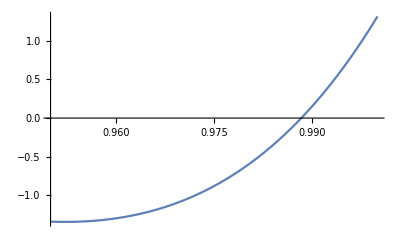

```mathematica
l = 10;
n = 2;
nn = norm[n,l];
Plot[Worland[r,n,l]/nn,{r,0.95,1},PlotRange->All]
```

```mathematica
l = 10;
n = 2;
nn = norm[n,l]^2;
A=Table[Integrate[(2 r^2-1)Worland[r, n+i, l] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={2 n (l+n-1)/((l+2 n-2) (l+2 n-1)),l (l-1)/((l+2 n-1) (l+2 n+1)),(2 n+1) (2 l+2 n+1)/(2 (l+2 n+1) (l+2 n+2))}
A[[2;;4]]-B
```

{0,11/39,6/13,25/96,0}

{11/39,6/13,25/96}

{0,0,0}

```mathematica
l = 10;
n = 1;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4 r/r^l Worland[r, n+i, l],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={2 (l+n-1)/((l+2 n-2) (l+2 n-1)),-2 l/((l+2 n-1) (l+2 n+1)),-(2 n+1) (2 l+2 n+1)/(2 (l+n) (l+2 n+1) (l+2 n+2))
}
A[[2;;-2]]-B
```

{0,2/11,-20/143,-69/4004,0}

{2/11,-20/143,-69/4004}

{0,0,0}

```mathematica
l = 10;
n=2;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4 r/r^l Worland[r, n+i, l],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,3}]
B={4 (l+n-2) (l+n-1)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-8 l (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),2 (2 l^2-4 l n-4 n^2+1)/((l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),2 l (2 n+1) (2 l+2 n+1)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),(2 n+1) (2 n+3) (2 l+2 n+1) (2 l+2 n+3)/(4 (l+n) (l+n+1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4))}
A[[2;;-2]]-B
```

{0,1/39,-4/117,7/1248,125/31824,175/339456,0}

{1/39,-4/117,7/1248,125/31824,175/339456}

{0,0,0,0,0}

```mathematica
l = 10;
n=4;
nn=norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4r)/r^l Worland[r, n+i, l],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-5,5}]
B={16 (l+n-4) (l+n-3) (l+n-2) (l+n-1)/((l+2 n-8) (l+2 n-7) (l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-64 l (l+n-3) (l+n-2) (l+n-1)/((l+2 n-7) (l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),16 (l+n-2) (l+n-1) (6 l^2-4 l n+4 l-4 n^2+8 n+5)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),-16 l (l+n-1) (4 l^2-12 l n+6 l-12 n^2+12 n+17)/((l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),2 (8 l^4-96 l^3 n-48 l^2 n^2+100 l^2+96 l n^3-120 l n+48 n^4-120 n^2+27)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4)),4 l (2 n+1) (2 l+2 n+1) (4 l^2-12 l n-6 l-12 n^2-12 n+17)/((l+n) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5)),(2 n+1) (2 n+3) (2 l+2 n+1) (2 l+2 n+3) (6 l^2-4 l n-4 l-4 n^2-8 n+5)/((l+n) (l+n+1) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6)),l (2 n+1) (2 n+3) (2 n+5) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5)/((l+n) (l+n+1) (l+n+2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6) (l+2 n+7)),(2 n+1) (2 n+3) (2 n+5) (2 n+7) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5) (2 l+2 n+7)/(16 (l+n) (l+n+1) (l+n+2) (l+n+3) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6) (l+2 n+7) (l+2 n+8))}
A[[2;;-2]]-B
```

{0,1/3570,-4/6783,151/452200,1/19380,-263/4341120,-957/58243360,92597/18637875200,128557/46594688000,29667/85201715200,0}

{1/3570,-4/6783,151/452200,1/19380,-263/4341120,-957/58243360,92597/18637875200,128557/46594688000,29667/85201715200}

{0,0,0,0,0,0,0,0,0}

```mathematica
lapl[f_,l_]:=(1/r^2 D[r^2 D[f,r],r]-(l(l+1))/r^2 f)
bilapl[f_,l_]:=lapl[lapl[f,l],l]
```

```mathematica
l = 10;
n=2;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[(4 r)/r^l lapl[Worland[r, n+i, l],l],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,2}]
B={8 (l+n-1) (2 l+2 n-1)/((l+2 n-2) (l+2 n-1)),8 (4 l n+4 n^2-1)/((l+2 n-1) (l+2 n+1)),2 (2 n+1)^2 (2 l+2 n+1)/((l+n) (l+2 n+1) (l+2 n+2))}
A[[2;;-2]]-B
```

{0,506/39,152/39,125/288,0}

{506/39,152/39,125/288}

{0,0,0}

```mathematica
l = 10;
n=4;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^l lapl[Worland[r, n+i, l],l],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-4,4}]
B={32 (l+n-3) (l+n-2) (l+n-1) (2 l+2 n-5)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-32 (l+n-2) (l+n-1) (4 l^2-6 l-4 n^2+8 n+5)/((l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),8 (l+n-1) (8 l^3-40 l^2 n-4 l^2-56 l n^2+80 l n+62 l-8 n^3+36 n^2-22 n-21)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),16 (16 l^3 n+4 l^3-24 l^2 n-24 l^2-32 l n^3-24 l n^2+40 l n+14 l-16 n^4+40 n^2-9)/((l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)) ,2 (2 n+1) (2 l+2 n+1) (48 l^2 n+48 l^2+32 l n^2+8 l n-84 l-8 n^3-36 n^2-22 n+21)/((l+n) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4)),2 (2 n+1) (2 n+3) (2 l+2 n+1) (2 l+2 n+3) (8 l n+14 l+4 n^2+8 n-5)/((l+n) (l+n+1) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5)),(2 n+1) (2 n+3) (2 n+5)^2 (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5)/(2 (l+n) (l+n+1) (l+n+2) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6))}
A[[2;;-2]]-B
```

{0,253/1785,-1252/11305,-1859/28560,1997/135660,43413/2025856,26071/3831800,1671241/2192691200,0}

{253/1785,-1252/11305,-1859/28560,1997/135660,43413/2025856,26071/3831800,1671241/2192691200}

{0,0,0,0,0,0,0}

```mathematica
l = 10;
n=4;
nn=norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^l(bilapl[Worland[r, n+i, l],l]//Simplify//Expand),r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,3}]
B={64 (l+n-2) (l+n-1) (2 l+2 n-5) (2 l+2 n-3)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),128 (l+n-1) (2 l+2 n-3) (4 l n+4 n^2-4 n-3)/((l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),96 (2 n+1) (2 l+2 n-1) (4 l n+2 l+4 n^2-5)/((l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),32 (2 n+1) (2 n+3) (2 l+2 n+1) (4 l n+4 l+4 n^2+4 n-3)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),4 (2 n+1) (2 n+3)^2 (2 n+5) (2 l+2 n+1) (2 l+2 n+3)/((l+n) (l+n+1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4))}
A[[2;;-2]]-B
```

{0,11960/119,106600/969,174231/3230,1060356/79135,128557/93100,0}

{11960/119,106600/969,174231/3230,1060356/79135,128557/93100}

{0,0,0,0,0}

```mathematica
corQm[f_,l_]:=D[f,r] -(l-1) f/r
corQp[f_,l_]:=-(l(l+2)(l+m+1))/(2l+3)D[f,r] -(l(l+2)^2(l+m+1))/(2l +3)f/r
```

```mathematica
l = 10;
n=4;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[(4 r)/r^l corQm[Worland[r, n+i, l-1],l],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-2,3}]
B={8 (l+n-2) (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1)),-4 (l+n-1) (2 l-2 n-1)/((l+2 n-2) (l+2 n-1) (l+2 n+1)),-2 (2 n+1) (4 l+2 n-1)/((l+2 n-1) (l+2 n+1) (l+2 n+2)),-(2 n+1) (2 n+3) (2 l+2 n+1)/((l+n) (l+2 n+1) (l+2 n+2) (l+2 n+3))}
A[[2;;-2]]-B
```

{0,26/85,-143/1292,-423/3230,-957/37240,0}

{26/85,-143/1292,-423/3230,-957/37240}

{0,0,0,0}

```mathematica
l = 10;
n=4;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[(4 r)/r^(l+1)Worland[r, n+i, l+1],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,2}]
B = {4 n (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1))-4 (n-1) (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1)),2 (2 l^2+2 l n-3 l+2 n^2-3 n-2)/((l+2 n-2) (l+2 n-1) (l+2 n+1))-2 (2 l^2+2 l n+l+2 n^2-n-1)/((l+2 n-2) (l+2 n-1) (l+2 n+1)),-(2 l+2 n+1) (2 l^2+2 l n+2 n^2+3 n-2)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2))+(2 l+2 n+1) (2 l^2+2 l n+2 l+2 n^2+n-1)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2)),-(2 n+1) (2 l+2 n+1) (2 l+2 n+3)/(2 (l+n+1) (l+2 n+1) (l+2 n+2) (l+2 n+3))+(2 n+1) (2 l+2 n+1) (2 l+2 n+3)/(2 (l+n) (l+2 n+1) (l+2 n+2) (l+2 n+3))}
A[[2;;-2]]-B
```

{0,13/1020,-49/2584,377/90440,899/372400,0}

{13/1020,-49/2584,377/90440,899/372400}

{0,0,0,0}

```mathematica
l = 10;
n=4;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[(4 r)/r^l D[Worland[r, n+i, l+1],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-3,2}]
B={4 n (l-1) (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1))-4 (l-3) (n-1) (l+n-1)/((l+2 n-3) (l+2 n-2) (l+2 n-1)),-2 (l-3) (2 l^2+2 l n+l+2 n^2-n-1)/((l+2 n-2) (l+2 n-1) (l+2 n+1))+2 (l-1) (2 l^2+2 l n-3 l+2 n^2-3 n-2)/((l+2 n-2) (l+2 n-1) (l+2 n+1)),(l-3) (2 l+2 n+1) (2 l^2+2 l n+2 l+2 n^2+n-1)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2))-(l-1) (2 l+2 n+1) (2 l^2+2 l n+2 n^2+3 n-2)/((l+n) (l+2 n-1) (l+2 n+1) (l+2 n+2)),(l-3) (2 n+1) (2 l+2 n+1) (2 l+2 n+3)/(2 (l+n) (l+2 n+1) (l+2 n+2) (l+2 n+3))-(l-1) (2 n+1) (2 l+2 n+1) (2 l+2 n+3)/(2 (l+n+1) (l+2 n+1) (l+2 n+2) (l+2 n+3))}
A[[2;;-2]]-B
```

{0,13/68,193/2584,-2291/12920,-2697/53200,0}

{13/68,193/2584,-2291/12920,-2697/53200}

{0,0,0,0}

```mathematica
l = 10;
n=4;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^l corQm[Worland[r, n+i, l-1],l],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-4,5}]
B={32 (l+n-4) (l+n-3) (l+n-2) (l+n-1)/((l+2 n-7) (l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-16 (l+n-3) (l+n-2) (l+n-1) (6 l-2 n-1)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),24 (l+n-2) (l+n-1) (4 l^2-8 l n-4 n^2+8 n+5)/((l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),-4 (l+n-1) (8 l^3-72 l^2 n-12 l^2-24 l n^2+72 l n+58 l+24 n^3+12 n^2-54 n-27)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),-2 (2 n+1) (32 l^3-48 l^2 n-72 l^2-96 l n^2-48 l n+112 l-24 n^3+12 n^2+54 n-27)/((l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4)),-3 (2 n+1) (2 n+3) (2 l+2 n+1) (8 l^2-8 l-4 n^2-8 n+5)/((l+n) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5)),-(2 n+1) (2 n+3) (2 n+5) (2 l+2 n+1) (2 l+2 n+3) (8 l+2 n-1)/(2 (l+n) (l+n+1) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6)),-(2 n+1) (2 n+3) (2 n+5) (2 n+7) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5)/(4 (l+n) (l+n+1) (l+n+2) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6) (l+2 n+7))}
A[[2;;-2]]-B
```

{0,2/357,-11/1330,159/226100,2587/1085280,213/723520,-9657/27408640,-338923/2329734400,-385671/21926912000,0}

{2/357,-11/1330,159/226100,2587/1085280,213/723520,-9657/27408640,-338923/2329734400,-385671/21926912000}

{0,0,0,0,0,0,0,0}

```mathematica
l = 10;
n=5;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^(l+1)Worland[r, n+i, l+1],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-5,4}]
B={16 (l+n-3) (l+n-2) (l+n-1)/((l+2 n-7) (l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),
-8 (l+n-2) (l+n-1) (8 l+2 n+1)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),
12 (l+n-1) (8 l^2+8 l-4 n^2+8 n+5)/((l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),-2 (32 l^3-48 l^2 n+72 l^2-96 l n^2+48 l n+112 l-24 n^3-12 n^2+54 n+27)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),(2 l+2 n+1) (8 l^3-72 l^2 n+12 l^2-24 l n^2-72 l n+58 l+24 n^3-12 n^2-54 n+27)/((l+n) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4)),3 (2 n+1) (2 l+2 n+1) (2 l+2 n+3) (4 l^2-8 l n-4 n^2-8 n+5)/(2 (l+n) (l+n+1) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5)),(2 n+1) (2 n+3) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5) (6 l-2 n+1)/(4 (l+n) (l+n+1) (l+n+2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6)),(2 n+1) (2 n+3) (2 n+5) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5) (2 l+2 n+7)/(8 (l+n) (l+n+1) (l+n+2) (l+n+3) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6) (l+2 n+7))}
A[[2;;-2]]-B
```

{0,2/14535,-169/523260,5/23256,251/14976864,-10447/224652960,-341/78310400,341/67123200,12617/11675197440,0}

{2/14535,-169/523260,5/23256,251/14976864,-10447/224652960,-341/78310400,341/67123200,12617/11675197440}

{0,0,0,0,0,0,0,0}

```mathematica
l = 4;
n=7;
nn = norm[n,l]^2;
A=Table[Integrate[r^l Integrate[4r Integrate[4r Integrate[4r Integrate[(4 r)/r^l D[Worland[r, n+i, l+1],r],r],r],r],r] Worland[r,n,l]/(√(1-r^2)),{r,0,1}]/nn,{i,-5,4}]
B={16 (l+n-3) (l+n-2) (l+n-1)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1)),-8 (l+n-2) (l+n-1) (4 l^2+6 l n-33 l-4 n^2+8 n+5)/((l+2 n-6) (l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1)),-12 (l+n-1) (8 l^2 n+20 l^2+20 l n^2-32 l n-5 l+8 n^3-28 n^2+14 n+15)/((l+2 n-5) (l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2)),2 (16 l^4+80 l^3 n+104 l^3+96 l^2 n^2-144 l^2 n-16 l^2-24 l n^3-204 l n^2+118 l n+139 l-48 n^4+120 n^2-27)/((l+2 n-4) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3)),-(2 l+2 n+1) (8 l^4-8 l^3 n+44 l^3-120 l^2 n^2-264 l^2 n-14 l^2-168 l n^3-204 l n^2+122 l n+139 l-48 n^4+120 n^2-27)/((l+n) (l+2 n-3) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4)),-3 (2 n+1) (2 l+2 n+1) (2 l+2 n+3) (4 l^3+8 l^2 n+24 l^2-4 l n^2-24 l n-19 l-8 n^3-28 n^2-14 n+15)/(2 (l+n) (l+n+1) (l+2 n-2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5)),-(2 n+1) (2 n+3) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5) (6 l^2+14 l n+41 l+4 n^2+8 n-5)/(4 (l+n) (l+n+1) (l+n+2) (l+2 n-1) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6)),-(2 n+1) (2 n+3) (2 n+5) (2 l+2 n+1) (2 l+2 n+3) (2 l+2 n+5) (2 l+2 n+7)/(8 (l+n) (l+n+1) (l+n+2) (l+n+3) (l+2 n+1) (l+2 n+2) (l+2 n+3) (l+2 n+4) (l+2 n+5) (l+2 n+6))}
A[[2;;-2]]-B
```

{0,2/1547,5/33592,-163/67184,-139/434112,764359/525275520,104875/280146944,-67425/214230016,-36975/315707392,0}

{2/1547,5/33592,-163/67184,-139/434112,764359/525275520,104875/280146944,-67425/214230016,-36975/315707392}

{0,0,0,0,0,0,0,0}

```mathematica
lapl[lapl[r^m f[r],m],m]/r^m//Simplify//Expand
```

-(4 m f'[r])/r^3-(4 m^2 f'[r])/r^3+(4 m f''[r])/r^2+(4 m^2 f''[r])/r^2+(4 f^(3)[r])/r+(4 m f^(3)[r])/r+f^(4)[r]

```mathematica
a1=4 √((x+1)/2)D[4 √((x+1)/2)D[4 √((x+1)/2)D[4 √((x+1)/2)D[f[x],x],x],x],x]//FullSimplify
```

16 (3 f''[x]+4 (1+x) (3 f^(3)[x]+(1+x) f^(4)[x]))

```mathematica
a2=4D[4 √((x+1)/2)D[4 √((x+1)/2)D[f[x],x],x],x]//FullSimplify
```

48 f''[x]+32 (1+x) f^(3)[x]

```mathematica
a3=4D[4D[f[x],x],x]
```

16 f''[x]

```mathematica
a1 + 4(m+1)a2+4m(m+1)a3//Expand
a1 + 4(m+1)a2+4m(m+1)a3//FullSimplify
```

240 f''[x]+256 m f''[x]+64 m^2 f''[x]+320 f^(3)[x]+128 m f^(3)[x]+320 x f^(3)[x]+128 m x f^(3)[x]+64 f^(4)[x]+128 x f^(4)[x]+64 x^2 f^(4)[x]

16 (3+2 m) (5+2 m) f''[x]+64 (1+x) ((5+2 m) f^(3)[x]+(1+x) f^(4)[x])